

```mathematica
Plot[Sin[t],{t,0,2 Pi}]
```

```mathematica
tunnelwidth = 0.2;
R = 10;
z[R_,d_]:=Sqrt[R^2 -d^2]; 
Manipulate[Graphics[{Circle[{0,0},R],
Point[{0,R Cos[t]}],Point[{d,z[R,d]Cos[t]}],
Line[{{tunnelwidth,-R},{tunnelwidth,R}}],Line[{{-tunnelwidth,-R},{-tunnelwidth,R}}], Line[{{d+tunnelwidth,-z[R,d+tunnelwidth]},{d+tunnelwidth,z[R,d+tunnelwidth]}}],Line[{{d-tunnelwidth,-z[R,d-tunnelwidth]},{d-tunnelwidth,z[R,d-tunnelwidth]}}]}],{t,0,2 Pi},{d,0,R}]
```

```mathematica
Eff =Import["/home/nicolas/Documents/Physics/Bachelors-Dissertation/Trajectories/data.csv", "Table"];
EffectiveTrajectory = Interpolation[Eff,InterpolationOrder->5]
```

InterpolatingFunction[…]

```mathematica
EffectiveTrajectory[5.6]
```

9.99766

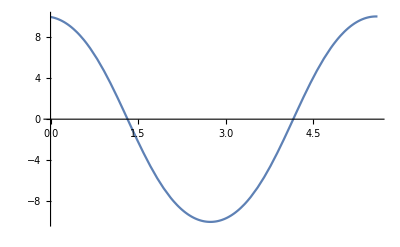

```mathematica
Plot[EffectiveTrajectory[t],{t,0,5.6}]
```

```mathematica
Manipulate[Graphics[{Circle[{0,0},10],
Point[{0,EffectiveTrajectory[t]}],Style[Point[{0,R Cos[t]}],Red],
Line[{{tunnelwidth,-R},{tunnelwidth,R}}],Line[{{-tunnelwidth,-R},{-tunnelwidth,R}}]
}],{t,0, 5.6}]
```